```mathematica
MainFunc[mF_,nF_]:=Module[{i,j,k,m,n},
m=mF;n=nF;
Φ0[p_,r_]=BesselI[0,p*r];
Φ1[p_,r_]=D[Φ0[p,r],{r,1}];
Ψ0[q_,r_]=BesselI[0,q*r]/(q*BesselI[1,q*R1]+αDivλ*BesselI[0,q*R1])+BesselK[0,q*r]/(q*BesselK[1,q*R1]-αDivλ*BesselK[0,q*R1]);
Ψ1[q_,r_]=D[Ψ0[q,r],{r,1}];
p0Appr=√(αDivλ/H)*(1-1/6*H*αDivλ+11/360*H^2*αDivλ^2-17/5040*H^3*αDivλ^3-281/604800*H^4*αDivλ^4+44029/119750400*H^5*αDivλ^5);
μ00=1/2*(H+αDivλ*Cos[p0Appr*H]^2/p0Appr^2);
mp={p0Appr};
mμ={μ00};
For[i=1,i≤m,i++,
iπ=i*π;
piAppr=iπ/H+αDivλ/iπ-(H αDivλ^2)/iπ^3-(H^2 (-6+iπ^2) αDivλ^3)/(3 iπ^5)+(H^3 (-15+4 iπ^2) αDivλ^4)/(3 iπ^7);
AppendTo[mp,piAppr];
μii=1/2*(H+αDivλ*Cos[piAppr*H]^2/piAppr^2);
AppendTo[mμ,μii];
];
q0Appr=√((2*αDivλ)/H)*(1-1/12*H αDivλ+11/1440*H^2 αDivλ^2-17/40320*H^3 αDivλ^3-281/9676800*H^4 αDivλ^4+44029/3832012800*H^5 αDivλ^5);
ν00=1/2*(H*(1+αDivλ^2/q0Appr^2)+αDivλ/q0Appr^2*(1+((q0Appr^2+αDivλ^2)/(q0Appr^2-αDivλ^2))^2*Cos[q0Appr*H]^2));
mν={ν00};
mq={q0Appr};
For[j=1,j≤n,j++,
jπ=j*π;
qjAppr=jπ/H+(2 αDivλ)/jπ-(4 H αDivλ^2)/jπ^3-(2 H^2 (-24+jπ^2) αDivλ^3)/(3 jπ^5)+(16 H^3 (-15+jπ^2) αDivλ^4)/(3 jπ^7);
AppendTo[mq,qjAppr];
νjj=1/2*(H*(1+αDivλ^2/qjAppr^2)+αDivλ/qjAppr^2*(1+((qjAppr^2+αDivλ^2)/(qjAppr^2-αDivλ^2))^2*Cos[qjAppr*H]^2));
AppendTo[mν,νjj];
];
mκ=Table[0,{i,0,m},{j,0,n}];
For[i=0,i≤m,i++,
For[j=0,j≤n,j++,
κij=αDivλ/(mq[[j+1]]^2-mp[[i+1]]^2);
mκ[[i+1,j+1]]=κij;
];
];
mA=Table[0,{i,1,m+n+2},{j,1,m+n+2}];
mB=Table[0,{i,1,m+n+2}];
For[k=1,k≤m+1,k++,
mA[[k,k]]=Φ0[mp[[k]],R0]/Φ1[mp[[k]],R0]*mμ[[k]];
For[j=0,j≤n,j++,
mA[[k,j+m+2]]=-Ψ0[mq[[j+1]],R0]/Ψ1[mq[[j+1]],R0]*mκ[[k,j+1]];
];
mB[[k]]=-1/(λ*mp[[k]]^2)
];
For[k=m+2,k≤m+n+2,k++,
mA[[k,k]]=-mν[[k-m-1]];
For[i=0,i≤m,i++,
mA[[k,i+1]]=mκ[[i+1,k-m-1]];
];
];
mX=LinearSolve[mA,mB];
s=0;
For[i=0,i≤m,i++,
s+=mX[[i+1]]/mp[[i+1]]^2
];
ΘAvg=s*2/R0+1/α+H/λ;
RH=ΘAvg/(π*R0^2);
Print["R1=",R1,"  RH=",RH];
]
```

```mathematica
MyLinearSolve[a_, b_] := Module[ {i, j, n, k, m, max },
n = Dimension[a, 1];
For[k=1,k≤n,k++,
m=k;
max=Abs[a[[k,k]]];
For[i=k+1,i≤n,i++,
If[Abs[a[[i,k]]]>max,
{m=i,max=Abs[a[[i,k]]]}]
];
If[m≠k,
For[j=k,j≤n+1,j++,
{w=a[[k,j]],a[[k,j]]=a[[m,j]],a[[m,j]]=w}
]
];
For[j=n+1,j≥k,j--,
a[[k,j]]=a[[k,j]]/a[[k,k]]
];
For[i=1,i≤n,i++,
If[i≠k,
For[j=n+1,j≥k,j--,
a[[i,j]]=a[[i,j]]-a[[i,k]]*a[[k,j]]
]
]
];
Print[a//MatrixForm]]
]
```

```mathematica
MyLinearSolve[{{2,3},{7,8}}, {2, 1}]
```

```mathematica
MainCircle[mF_,nF_]:=Module[{},
α=10.0;
λ=236;
αDivλ=α/λ;
H=0.003;
R0=0.01;R1=0.05;
VN=π*R1^2*H;
VN=0.00002;
Print["VN=",VN];
bWas=False;
mG={};
For[R1=0.05,R1≤0.14,R1+=0.002,
H=VN/(π*R1^2);
MainFunc[mF,nF];
If[bWas,
If[RHMin>RH,
R1Min=R1;RHMin=RH;
];
,
R1Min=R1;RHMin=RH;
bWas=True;
];
AppendTo[mG,{R1,RH}];
];
HMin=VN/(π*R1Min^2);
Print["R1Min=",R1Min,"  HMin=",HMin,"  RHMin=",RHMin];
ListPlot[mG,PlotJoined->True];
]
```

```mathematica
MainCircle[5,5]
mG0505=mG;
Put[mG0505,"G0505.txt"];
G0505=ListPlot[mG0505,PlotJoined->True,PlotStyle->{RGBColor[1,0,1],Thickness[0.003]},ImageSize->100];
```

VN=0.00002

R1=0.05  RH=64.0857

R1=0.052  RH=65.3265

R1=0.054  RH=66.5226

R1=0.056  RH=67.6766

R1=0.058  RH=68.7908

R1=0.06  RH=69.8673

R1=0.062  RH=70.9083

R1=0.064  RH=71.9156

R1=0.066  RH=72.8909

R1=0.068  RH=73.8359

R1=0.07  RH=74.7522

R1=0.072  RH=75.6411

R1=0.074  RH=76.5041

R1=0.076  RH=77.3423

R1=0.078  RH=78.157

R1=0.08  RH=78.9494

R1=0.082  RH=79.7203

R1=0.084  RH=80.4709

R1=0.086  RH=81.2021

R1=0.088  RH=81.9147

R1=0.09  RH=82.6096

R1=0.092  RH=83.2875

R1=0.094  RH=83.9493

R1=0.096  RH=84.5955

R1=0.098  RH=85.2269

R1=0.1  RH=85.8441

R1=0.102  RH=86.4477

R1=0.104  RH=87.0383

R1=0.106  RH=87.6163

R1=0.108  RH=88.1824

R1=0.11  RH=88.7369

R1=0.112  RH=89.2804

R1=0.114  RH=89.8133

R1=0.116  RH=90.336

R1=0.118  RH=90.8489

R1=0.12  RH=91.3524

R1=0.122  RH=91.8469

R1=0.124  RH=92.3327

R1=0.126  RH=92.8101

R1=0.128  RH=93.2794

R1=0.13  RH=93.741

R1=0.132  RH=94.1952

R1=0.134  RH=94.6421

R1=0.136  RH=95.0822

R1=0.138  RH=95.5156

R1=0.14  RH=95.9425

R1Min=0.05  HMin=0.00254648  RHMin=64.0857

```mathematica
MainCircle[10,10]
mG1010=mG;
Put[mG1010,"G1010.txt"];
G1010=ListPlot[mG1010,PlotJoined->True,PlotStyle->{RGBColor[1,1,0],Thickness[0.003]},ImageSize->100];
```

VN=0.00002

R1=0.05  RH=64.0857

R1=0.052  RH=65.3265

R1=0.054  RH=66.5226

R1=0.056  RH=67.6766

R1=0.058  RH=68.7908

R1=0.06  RH=69.8673

R1=0.062  RH=70.9083

R1=0.064  RH=71.9156

R1=0.066  RH=72.8909

R1=0.068  RH=73.8359

R1=0.07  RH=74.7522

R1=0.072  RH=75.6411

R1=0.074  RH=76.5041

R1=0.076  RH=77.3423

R1=0.078  RH=78.157

R1=0.08  RH=78.9494

R1=0.082  RH=79.7203

R1=0.084  RH=80.4709

R1=0.086  RH=81.2021

R1=0.088  RH=81.9147

R1=0.09  RH=82.6096

R1=0.092  RH=83.2875

R1=0.094  RH=83.9493

R1=0.096  RH=84.5955

R1=0.098  RH=85.2269

R1=0.1  RH=85.8441

R1=0.102  RH=86.4477

R1=0.104  RH=87.0383

R1=0.106  RH=87.6163

R1=0.108  RH=88.1824

R1=0.11  RH=88.7369

R1=0.112  RH=89.2804

R1=0.114  RH=89.8133

R1=0.116  RH=90.336

R1=0.118  RH=90.8489

R1=0.12  RH=91.3524

R1=0.122  RH=91.8469

R1=0.124  RH=92.3327

R1=0.126  RH=92.8101

R1=0.128  RH=93.2794

R1=0.13  RH=93.741

R1=0.132  RH=94.1952

R1=0.134  RH=94.6421

R1=0.136  RH=95.0822

R1=0.138  RH=95.5156

R1=0.14  RH=95.9425

R1Min=0.05  HMin=0.00254648  RHMin=64.0857

```mathematica
mG0505=Get["G0505.txt"];
mG1010=Get["G1010.txt"];
```

```mathematica
mG050208=Get["G050208.txt"];
mG100416=Get["G100416.txt"];
mG150624=Get["G150624.txt"];
```

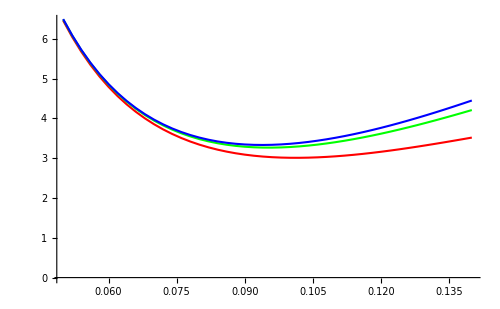

```mathematica
G050208=ListPlot[mG050208,PlotJoined->True,PlotStyle->{RGBColor[1,0,0],Thickness[0.003]},ImageSize->100];
G100416=ListPlot[mG100416,PlotJoined->True,PlotStyle->{RGBColor[0,1,0],Thickness[0.003]},ImageSize->100];
G150624=ListPlot[mG150624,PlotJoined->True,PlotStyle->{RGBColor[0,0,1],Thickness[0.003]},ImageSize->100];
Show[G050208,G100416,G150624,G0505,G1010,ImageSize->500]
```